```mathematica
DD[n_,k_] := Sum[ DD[n/j,k-1],{j,1,n}]
DD[n_,0] := 1
DD[100,4]
3575
PP[n_, k_, a_ ] := Sum[ a N[ MangoldtLambda[j]/Log[j]]( 1/(k!) + PP[n/j, k+1,a]),{j,2,n}]
PP[100,1,4]
P2[ n_, a_ ] := PP[n,1,a]
P2[ 100,3]
DD[100,3]
P2[100, I]
P3[n_, k_ ] := P2[n,k]/k
DiscretePlot[Re[ P3[j,I]+P3[j,-I]],{j,2,100}]
```

```mathematica
QQ[n_, k_, a_ ] := QQ[n,k,a]=Sum[ j^a ( 1/k - QQ[Floor[n/j], k+1,a]),{j,2,n}]
Q2[ n_, a_ ] := 1+QQ[n,1,-a]
Q3[n_, k_, j_ ]:=(Q2[ n, k+ j I]+Q2[n,k-j I])/2
```

```mathematica
QQ[100,.5, 1]
```

4438.86

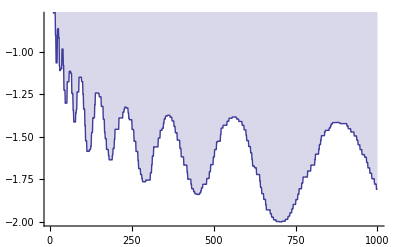

```mathematica
DiscretePlot[ Q3[n,.5,14.134725141734695 ],{n,2,1000}]
```

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ